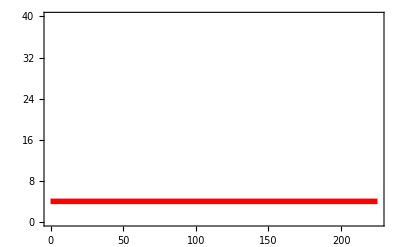
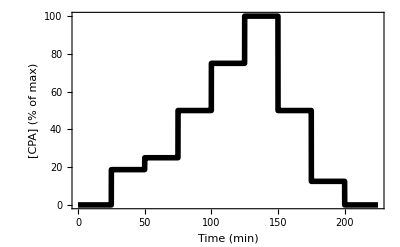
-Graphics--Graphics-CPA Exposure Profile 1

Progress = 33% for sample #1 of 1

Progress = 67% for sample #1 of 1

Progress = 100% for sample #1 of 1

-Graphics-

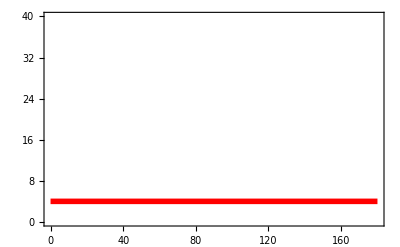
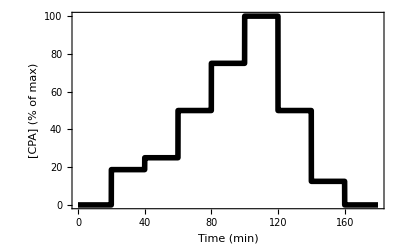
-Graphics--Graphics-CPA Exposure Profile 2

Progress = 33% for sample #1 of 1

Progress = 67% for sample #1 of 1

Progress = 100% for sample #1 of 1

-Graphics-

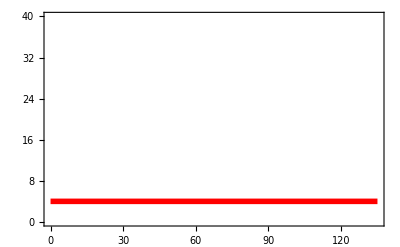
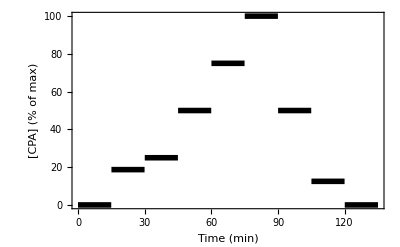
-Graphics--Graphics-CPA Exposure Profile 3

Progress = 33% for sample #1 of 1

Progress = 67% for sample #1 of 1

Progress = 100% for sample #1 of 1

-Graphics-

-Graphics-

Null

```mathematica
(*Validating cartesian simulation by comparing to Zonghu's result (Han 2020)*)
(*Note: There is a different version of this in tissue_CPA_dif_dev.nb*)
Clear["Global`*"]
SetOptions[Plot,BaseStyle->FontSize->13];

(*inputs*)
thicknesses={
2
}*.001; (*m, thickness of arterial wall*)
profiles={
(*25 min steps: *)
{{{0,t<25*60},{18.7,t<50*60},{25,t<75*60},{50,t<100*60},{75,t<125*60},{100,t<150*60},{50,t<175*60},{12.5,t<200*60},{0,t<225*60}},4+273.15,225*60,9,6},
(*20 min steps: *)
{{{0,t<20*60},{18.7,t<40*60},{25,t<60*60},{50,t<80*60},{75,t<100*60},{100,t<120*60},{50,t<140*60},{12.5,t<160*60},{0,t<180*60}},4+273.15,180*60,9,6},
(*15 min steps: *)
{{{0,t<15*60},{18.7,t<30*60},{25,t<45*60},{50,t<60*60},{75,t<75*60},{100,t<90*60},{50,t<105*60},{12.5,t<120*60},{0,t<135*60}},4+273.15,135*60,9,6}
}; (*{c=f(t),T,ttot,nSteps,locLf}*) (*CM toxicity screening profile*)
cMax=8.41*1000; (*mM, max [CPA], DEP (51 w/v %), compare to 7.09 M for DEP (51 w/v %), 6.07 M for 47 w/v % DMSO*)
etas={0,.5,1}; (*normalized distance from the midline*)

(*constants*)
Rgas=8.3145; (*J/mol/K = N*m/mol/K, gas constant*)

(*parameters*)
DC=6.5*10^-11; (*cm^2/s, VS55 diffusivity in porcine arterial wall at 4 C (Han)*)
m=9; (*number of iterations for C=f(t)*)
n=3; (*number of iterations for C=f(r)*)
(*equations*)
L=thickness/2; (*m, characteristic length*)
x=eta*L+L; (*m, distance from midline, range of x = Subscript[L, c] to x = 2*Subscript[L, c]*)
(*initialization*)
table1={{"D (mm)","eta","c (M)","C (M)"}};
colors={Red,Blue,Black,Green,Purple,Orange,Brown,Yellow,Gray};

(*execution*)
nProfiles=Length[profiles];
ttotmax=Max[profiles[[All,3]]];
For[a=1,a<Length[thicknesses]+1,a++,
(*initialization*)
CPlotsL={}; (*plots of C vs x at the end of each step*)
(*execution*)
thickness=thicknesses[[a]];
For[b=1,b<nProfiles+1,b++,
(*c*)
cProfile=Piecewise[profiles[[b]][[1]]]*cMax/100; (*mM, c=f(t)*)
T=profiles[[b]][[2]]; (*K, T=f(t)*)
ttot=profiles[[b]][[3]]; (*s, total simulation time*)
nSteps=profiles[[b]][[4]]; (*number of c steps*)
locLf=profiles[[b]][[5]]; (*location of the final loading step*)
cProfile=cProfile/.t->t*60; (*for plotting in min*)
Print[Labeled[Overlay[{Plot[T-273.15,{t,0,ttot/60},PlotStyle->{Red,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,40},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},FrameLabel->{{None,"T (°C)"},{None,None}}],Plot[cProfile*100/cMax,{t,0,ttot/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{True,True,False,False},FrameStyle->{Automatic,Black,Automatic,Automatic},FrameLabel->{{"[CPA] (% of max)",None},{"Time (min)",None}}]}],"CPA Exposure Profile "<>ToString[b],Top]];
cProfile=cProfile/.t->t/60; (*converting back*)

(*C*)
(*initialization*)
Concs={}; (*C=f(t) at each eta value*)
CPlots={}; (*plots of C vs t at each eta value*)
(*execution*)
For[i=1,i<Length[etas]+1,i++,
eta=etas[[i]];
tPriorSteps=0; (*s, time of all the prior steps*)
ConcPW={}; (*C list to be input into piecewise function*)
C0=0; (*initial sample [CPA]*)
For[j=1,j<locLf+1,j++,
c=profiles[[b]][[1]][[j]][[1]]*cMax/100; (*mM, c for this step*)
tCurrentStep=profiles[[b]][[1]][[j]][[2,2]]; (*s, tf for this step*)
(*Print[DC[T]];*)

(*Calculating C = f(t)*)
sum1=0;
sum2=0;
For[k=1,k<m+1,k++,
sum1=sum1+(c*Cos[k*π]-c)/k Sin[k*π*x/thickness]Exp[-DC*k^2*π^2*(t-tPriorSteps)/thickness^2];
sum2=sum2+Sin[k*π*x/thickness]Exp[-DC*π^2*k^2*(t-tPriorSteps)/thickness^2]Integrate[C0*Sin[k*π*xp/thickness],{xp,0,thickness}];
];
Conc=c+2*sum1/π+2*sum2/thickness; (*mol/m^3, C=f(t)*)
(*Print[Plot[Conc/1000,{t,tPriorSteps,tCurrentStep},PlotRange->{0,cMax/1000},AxesLabel->{"t (s)","C (M)"},PlotLabel->"eta = "<>ToString[N[eta,2]]<>", c = "<>ToString[c/1000]<>" M",PlotStyle->colors[[j]]]];*)
(*Print[Conc];*)
AppendTo[ConcPW,{Conc,t<tCurrentStep}];
t=tCurrentStep;(*set t equal to the value at the end of the step*)
Cf=Quiet[Conc]; (*C at end of step*) (*this line triggers a precision warning for small thicknesses*)
AppendTo[table1,{thickness*1000,Round[eta,.01],c/1000,Round[Cf/1000,.01]}];
(*t=tStep*(j-1)+tOffset; (*C at beginning of step, offset to account for the inaccuracy of the solution at short times*)
Ci=Conc; (*C at beginning of step*)*)
Clear[t]; (*return t to a variable*)

(*Calculating C = f(r)*)
sum1=0;
sum2=0;
For[k=1,k<n+1,k++,
sum1=sum1+(c*Cos[k*π]-c)/k Sin[k*π*xp/thickness]Exp[-DC*k^2*π^2*(tCurrentStep-tPriorSteps)/thickness^2];
sum2=sum2+Sin[k*π*xp/thickness]Exp[-DC*π^2*k^2*(tCurrentStep-tPriorSteps)/thickness^2]Integrate[C0*Sin[k*π*xp/thickness],{xp,0,thickness}];
];
C0=c+2*sum1/π+2*sum2/thickness; (*C = f(x) at end of this step*)
(*Print[Plot[C0/1000,{rp,0,R},PlotRange->{0,cMax/1000},AxesLabel->{"r (m)","C (M)"},PlotStyle->colors[[j]]]];*)
tPriorSteps=profiles[[b]][[1]][[j]][[2,2]];
];

(*Plot C=f(t)*)
AppendTo[Concs,Piecewise[ConcPW]];
Concs=Concs/.t->t*60; (*for plotting in min*)
(*Print[Plot[Last[Concs]/1000,{t,0,tE/60},PlotRange->{0,cMax/1000},AxesLabel->{"t (min)","C (M)"},PlotLabel->"eta = "<>ToString[N[eta,2]]]];*)
If[i<Length[etas],
AppendTo[CPlots,Plot[Last[Concs]/1000,{t,0,ttot/60},PlotRange->{0,cMax/1000},PlotLabel->"thickness = "<>ToString[Round[thickness*1000,.1]]<>" mm",AxesLabel->{"t (min)","C (M)"},PlotStyle->colors[[i]]]];
,
AppendTo[CPlots,Plot[Last[Concs]/1000,{t,0,ttot/60},PlotRange->{0,cMax/1000},AxesLabel->{"t (min)","C (M)"},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,etas,LegendLabel->"eta",LegendFunction->Framed],{1,.6}]]];
];
Concs=Concs/.t->t/60; (*converting back*)

Print["Progress = "<>ToString[Round[100*i/Length[etas],1]]<>"% for sample #"<>ToString[a]<>" of "<>ToString[Length[thicknesses]]];
];(*end of i For loop*)
(*visualization*)
Print[Show[CPlots]];

(*Plot C=f(x)*)
C0=C0/.xp->xp/1000; (*for plotting in mm*)
(*Print[Plot[C0/1000,{xp,0,thickness*1000},PlotRange->{0,cMax/1000},AxesLabel->{"x (mm)","C (M)"}]];*)
If[b<nProfiles,
AppendTo[CPlotsL,Plot[100*C0/cMax,{xp,0,thickness*1000},PlotRange->{0,100},AxesLabel->{"x (mm)","C (% of max)"},PlotStyle->colors[[b]]]];
,
AppendTo[CPlotsL,Plot[100*C0/cMax,{xp,0,thickness*1000},PlotRange->{0,100},AxesLabel->{"x (mm)","C (% of max)"},PlotStyle->colors[[b]],PlotLabel->"thickness = "<>ToString[Round[thickness*1000,.1]]<>" mm",PlotLegends->Placed[LineLegend[colors,{25,20,15},LegendLabel->"Step Length (min)",LegendFunction->Framed],{1,.6}]]];
];
]; (*end of b For Loop*)
Print[Show[CPlotsL]];
]; (*end of a For Loop*)
```